```mathematica
比较单摆振动与正弦振动之间的差别
```

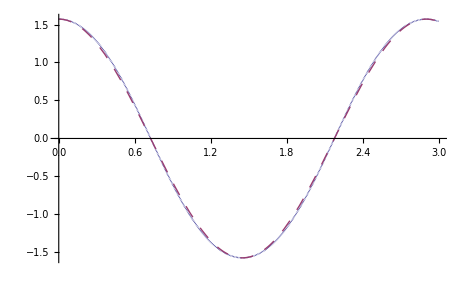

```mathematica
g=9.8;L=1.5;Ω=√(g/L);
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],
θ[0]==π/2,θ'[0]==0},θ,{t,0,10}];
θ=θ/.s[[1]];
θm1=FindMaximum[θ[t],{t,0.5}];
θm2=FindMaximum[θ[t],{t,3}];
T=(t/.θm2[[2]])-(t/.θm1[[2]]);
a=θm1[[1]];asin=a*Sin[(2π)/T*t+π/2];
Plot[{θ[t],asin},{t,0,3},
PlotStyle->{Dashing[{0,0}],
Dashing[{0.02,0.02}]},
AxesStyle->Thickness[0.003]]
Clear[g,L,Ω,s,θm1,θm2,θ,T,a,asin]
```